```mathematica
Variable Initialization;
Quit;$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
ClearAll["Global`*"];
e1=p1/(γ-1)+ρ1*u1*u1/2;
w11 = ρ1;
w21 = ρ1*u1;
w31 = e1;
w11p= ρ1;
w21p = u1;
w31p = p1;
W1={w11,w21,w31};
W1p={w11p,w21p,w31p};
SetAttributes[γ,Constant];
SetAttributes[r,Constant];
SetAttributes[cv,Constant];
SetAttributes[ρ1,Constant];
SetAttributes[u1,Constant];
SetAttributes[p1,Constant];
SetAttributes[ρ2,Constant];
SetAttributes[u2,Constant];
SetAttributes[p2,Constant];
SetAttributes[pt,Constant];
SetAttributes[tt,Constant];
SetAttributes[a2,Constant];
c1/:Dt[c1,u1]=0;c1/:Dt[c1,u2]=0;c2/:Dt[c2,u1]=0;c2/:Dt[c2,u2]=0;c1/:Dt[c1,ρ2]=0;c2/:Dt[c2,ρ1]=0;
c1/:Dt[c1,p2]=0;
c2/:Dt[c2,p1]=0;
eig1/:Dt[eig1,ρ1]=0;
eig1/:Dt[eig1,p1]=0;
eig1/:Dt[eig1,ρ2]=0;
eig1/:Dt[eig1,p2]=0;
```

```mathematica
c1= Sqrt[γ*p1/ρ1];
c2= Sqrt[γ*p2/ρ2];
t1 =c1*c1/(γ*r)
```

```mathematica
eig1 = (u1 + u2) / 2;
eig2 = eig1 + (c1 +c2)/2;
eig3 = eig1 - (c1 +c2)/2;
Dt[eig2,ρ1]
```

1/2 (Dt[c1,ρ1]+Dt[c2,ρ1])

```mathematica
R1=-eig1*(ρ1-ρ2-(p1-p2)/(c1*c1));
R2=-eig2*(p1-p2+(ρ1*c1)*(u1-u2));
R3=-eig3*(p1-p2-(ρ1*c1)*(u1-u2));
FullSimplify[Dt[R3,ρ1]]
FullSimplify[Dt[R3,u1]]
FullSimplify[Dt[R3,p1]]
FullSimplify[Dt[R3,ρ2]]
FullSimplify[Dt[R3,u2]]
FullSimplify[Dt[R3,p2]]
```

```mathematica
dp1dt= (R2+R3)/2;
```

```mathematica
dr1dt=R1+dp1dt/(c1*c1)
```

dp1dt/c1^2+R1

```mathematica
Dt[dr1dt,ρ1]
Dt[dr1dt,u1]
Dt[dr1dt,p1]
Dt[dr1dt,ρ2]
Dt[dr1dt,u2]
Dt[dr1dt,p2]
```

```mathematica
du1dt=(R2-dp1dt)/(ρ1*c1);
Dt[du1dt,ρ1]
Dt[du1dt,u1]
Dt[du1dt,p1]
Dt[du1dt,ρ2]
Dt[du1dt,u2]
Dt[du1dt,p2]
```

-(-dp1dt+R2)/(c1 ρ1^2)-((-dp1dt+R2) Dt[c1,ρ1])/(c1^2 ρ1)+(-Dt[dp1dt,ρ1]+Dt[R2,ρ1])/(c1 ρ1)

(-Dt[dp1dt,u1]+Dt[R2,u1])/(c1 ρ1)

-((-dp1dt+R2) Dt[c1,p1])/(c1^2 ρ1)+(-Dt[dp1dt,p1]+Dt[R2,p1])/(c1 ρ1)

(-Dt[dp1dt,ρ2]+Dt[R2,ρ2])/(c1 ρ1)

(-Dt[dp1dt,u2]+Dt[R2,u2])/(c1 ρ1)

(-Dt[dp1dt,p2]+Dt[R2,p2])/(c1 ρ1)

```mathematica
dru1dt = dr1dt*u1+du1dt*ρ1;
```

```mathematica
t1 = c1*c1/(γ*r);
c1 = Sqrt[γ * p/ρ];
e1 = ρ(cv*t1+u*u/2)
```

(u^2/2+(cv p)/(r ρ)) ρ

```mathematica
FullSimplify[Dt[e1,t]]
```

(cv Dt[p,t])/r+u ρ Dt[u,t]+1/2 u^2 Dt[ρ,t]

```mathematica
de1dt = dp1dt * cv/r + u1 * ρ1 * du1dt + u1 * u1 * dr1dt / 2;
Dt[de1dt,ρ1]
Dt[de1dt,u1]
Dt[de1dt,p1]
Dt[de1dt,ρ2]
Dt[de1dt,u2]
Dt[de1dt,p2]
```

-((-dp1dt+R2) u1 Dt[c1,ρ1])/c1^2+(cv Dt[dp1dt,ρ1])/r+1/2 u1^2 Dt[dr1dt,ρ1]+(u1 (-Dt[dp1dt,ρ1]+Dt[R2,ρ1]))/c1

(-dp1dt+R2)/c1+dr1dt u1+(cv Dt[dp1dt,u1])/r+1/2 u1^2 Dt[dr1dt,u1]+(u1 (-Dt[dp1dt,u1]+Dt[R2,u1]))/c1

-((-dp1dt+R2) u1 Dt[c1,p1])/c1^2+(cv Dt[dp1dt,p1])/r+1/2 u1^2 Dt[dr1dt,p1]+(u1 (-Dt[dp1dt,p1]+Dt[R2,p1]))/c1

(cv Dt[dp1dt,ρ2])/r+1/2 u1^2 Dt[dr1dt,ρ2]+(u1 (-Dt[dp1dt,ρ2]+Dt[R2,ρ2]))/c1

(cv Dt[dp1dt,u2])/r+1/2 u1^2 Dt[dr1dt,u2]+(u1 (-Dt[dp1dt,u2]+Dt[R2,u2]))/c1

(cv Dt[dp1dt,p2])/r+1/2 u1^2 Dt[dr1dt,p2]+(u1 (-Dt[dp1dt,p2]+Dt[R2,p2]))/c1

```mathematica
1-d1*(Sin[Pi*x^d2])^d3
f1=Dt[1-d1*(Sin[Pi*x^d2])^d3,d1,Constants->{d1,d2,d3,x}]
f2=Dt[1-d1*(Sin[Pi*x^d2])^d3,d2,Constants->{d1,d2,d3,x}]
f3=Dt[1-d1*(Sin[Pi*x^d2])^d3,d3,Constants->{d1,d2,d3,x}]
```

1-d1 Sin[π x^d2]^d3

-Sin[π x^d2]^d3

-d1 d3 π x^d2 Cos[π x^d2] Log[x] Sin[π x^d2]^(-1+d3)

-d1 Log[Sin[π x^d2]] Sin[π x^d2]^d3

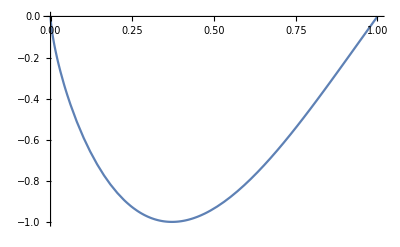

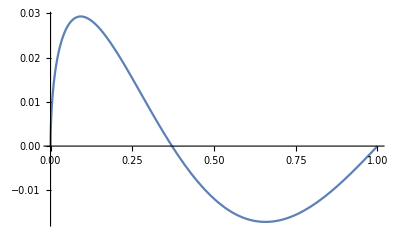

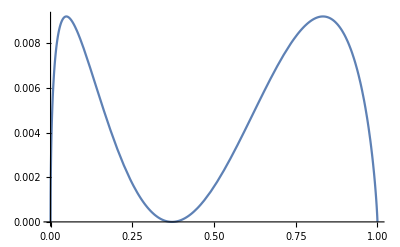

```mathematica
Plot[f1/.d1->0.025/.d2->0.7/.d3->1,{x,0,1}]
Plot[f2/.d1->0.025/.d2->0.7/.d3->1,{x,0,1}]
Plot[f3/.d1->0.025/.d2->0.7/.d3->1,{x,0,1}]
```

```mathematica
c1=Sqrt[γ*p1/ρ1]
dti=b/(u1+c1)
Dt[dti,{Wp1}].m
```

√((p1 γ)/ρ1)

b/(u1+√((p1 γ)/ρ1))

Dt[b,Wp1]/(u1+√((p1 γ)/ρ1)).m